rhoES

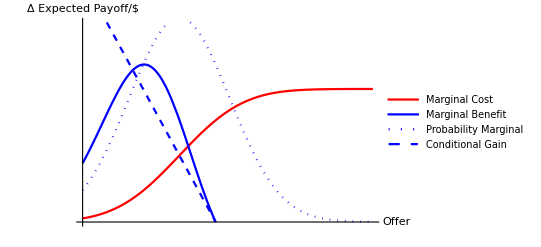

```mathematica
condMeanP[signal_,sRp_,rhoSeP_,meanP_]:=meanP+sRp *rhoSeP*signal
condSigP[sRp_,rhoSeP_]:=sRp*Sqrt[1-rhoSeP^2]
alpha[rhoES_,sEnv_,sRp_,rhoEnvRp_,rhoSeP_]:=sEnv*(rhoEnvRp-rhoES*rhoSeP)/(sRp*(1-rhoSeP^2))
a[meanE_,meanP_,signal_,rhoES_,sEnv_,sRp_,rhoEnvRp_,rhoSeP_]:=meanE+rhoES*sEnv*signal-alpha[rhoES,sEnv,sRp,rhoEnvRp,rhoSeP]*condMeanP[signal,sRp,rhoSeP,meanP]
pA[x_,meanE_,meanP_,signal_,rhoES_,sEnv_,sRp_,rhoEnvRp_,rhoSeP_]:=CDF[NormalDistribution[condMeanP[signal,sRp,rhoSeP,meanP],condSigP[sRp,rhoSeP]],x]
pM[x_,meanE_,meanP_,signal_,rhoES_,sEnv_,sRp_,rhoEnvRp_,rhoSeP_]:=PDF[NormalDistribution[condMeanP[signal,sRp,rhoSeP,meanP],condSigP[sRp,rhoSeP]],x]
condGain[x_,meanE_,meanP_,signal_,rhoES_,sEnv_,sRp_,rhoEnvRp_,rhoSeP_]:=a[meanE,meanP,signal,rhoES,sEnv,sRp,rhoEnvRp,rhoSeP]-(1-alpha[rhoES,sEnv,sRp,rhoEnvRp,rhoSeP])*x
MB[x_,meanE_,meanP_,signal_,rhoES_,sEnv_,sRp_,rhoEnvRp_,rhoSeP_]:=pM[x,meanE,meanP,signal,rhoES,sEnv,sRp,rhoEnvRp,rhoSeP]*condGain[x,meanE,meanP,signal,rhoES,sEnv,sRp,rhoEnvRp,rhoSeP]
rpf[x_,meanE_,meanP_,signal_,rhoES_,sEnv_,sRp_,rhoEnvRp_,rhoSeP_]:=pA[x,meanE,meanP,signal,rhoES,sEnv,sRp,rhoEnvRp,rhoSeP]*(meanE+rhoES*sEnv*signal-x)-sEnv*sRp*(rhoEnvRp-rhoES*rhoSeP)*pM[x,meanE,meanP,signal,rhoES,sEnv,sRp,rhoEnvRp,rhoSeP]

baseMeanE = 1; baseMeanP=.5; baseSEnv=1.5; baseSrp = .3; baseRhoES=.5; baseRhoSeP=.5;xMax =1.5;yRange={0,1.5};
plotStyleList = {Red,{Red,Dotted},{Red,Dashed},Blue,{Blue,Dotted},{Blue,Dashed}};
plotStyleList = {Red,Blue};
sigZVals = {-.5,0,.5}; rhoVals ={-.5,0,.5}; rhoES
baseMBvMCplot=Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoVals[[2]],baseRhoSeP],
MB[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoVals[[2]],baseRhoSeP],
pM[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoVals[[2]],baseRhoSeP],condGain[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoVals[[2]],baseRhoSeP]},
{x,0,xMax},PlotStyle->{Red,Blue,{Blue,Dotted},{Blue,Dashed}},PlotRange->yRange,Ticks->None,PlotLegends->{"Marginal Cost","Marginal Benefit","Probability Marginal","Conditional Gain"},AxesLabel->{ "Offer","Δ Expected Payoff/$"}]
```

## MB/MC Grid

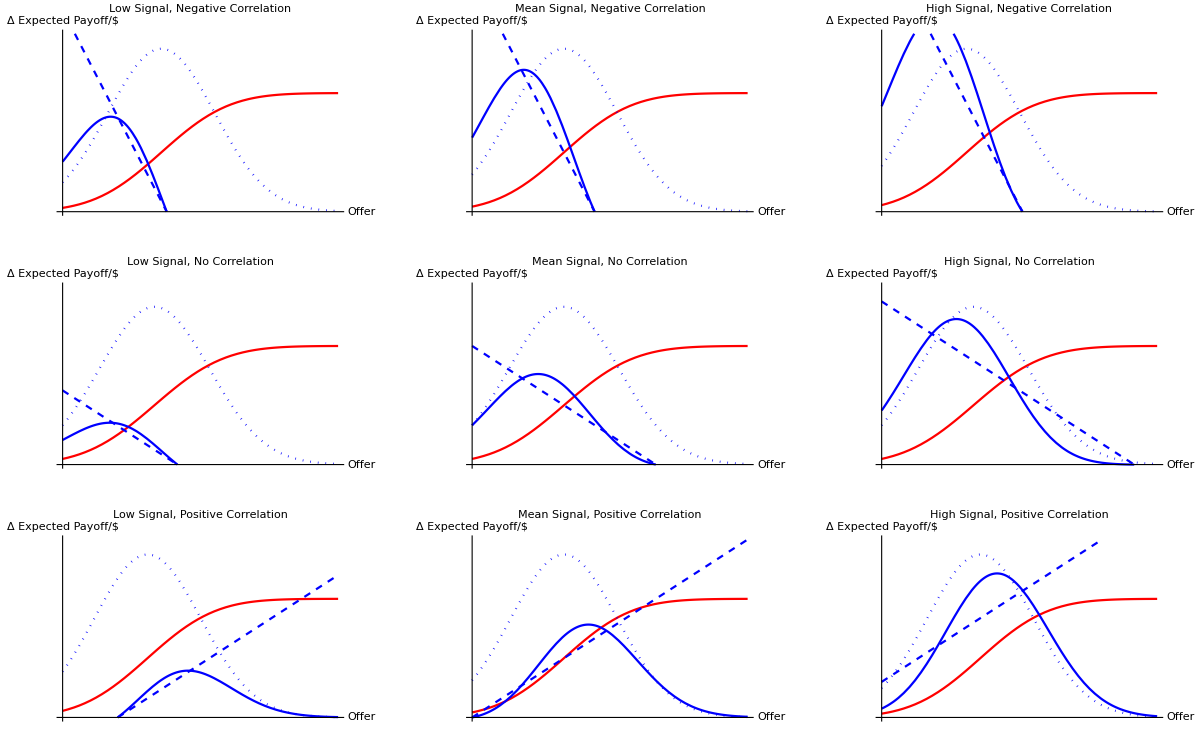

```mathematica
rhoEPVals = {-.5,0,.5}; rhoSPVals=rhoEPVals*baseRhoES;plotStyleList={Red,Blue,{Blue,Dotted},{Blue,Dashed}}; yRange={0,1.5}; 
plotOptions = {PlotStyle->plotStyleList,PlotRange->yRange,Ticks->None,AxesLabel->{"Offer","Δ Expected Payoff/$"}};
GraphicsGrid[{
{Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],pM[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],condGain[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Low Signal, Negative Correlation"],
Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],pM[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],condGain[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Mean Signal, Negative Correlation"],
Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],pM[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],condGain[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"High Signal, Negative Correlation"]},

{Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],pM[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],condGain[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Low Signal, No Correlation"],
Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],pM[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],condGain[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Mean Signal, No Correlation"],
Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],pM[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],condGain[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"High Signal, No Correlation"]},

{Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],pM[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],condGain[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Low Signal, Positive Correlation"],
Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],pM[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],condGain[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Mean Signal, Positive Correlation"],
Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],pM[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],condGain[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"High Signal, Positive Correlation"]}}
,ImageSize->Full]
```

## Marginal Cost

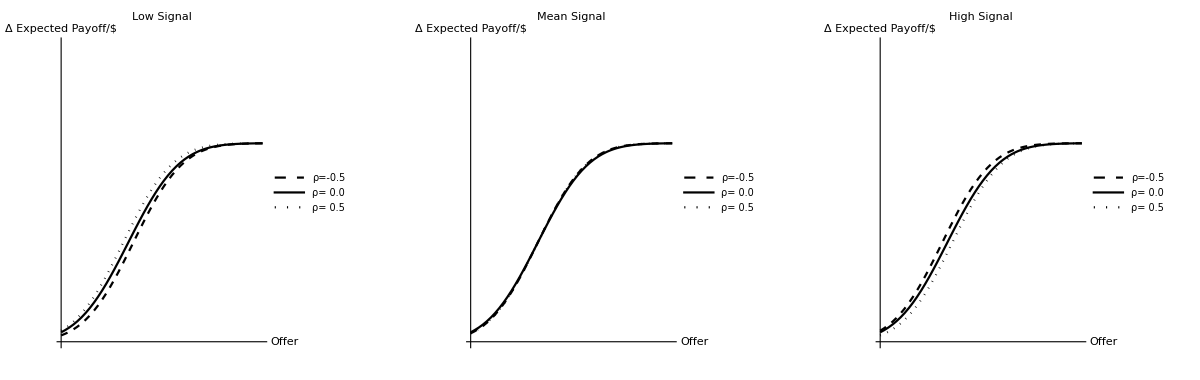

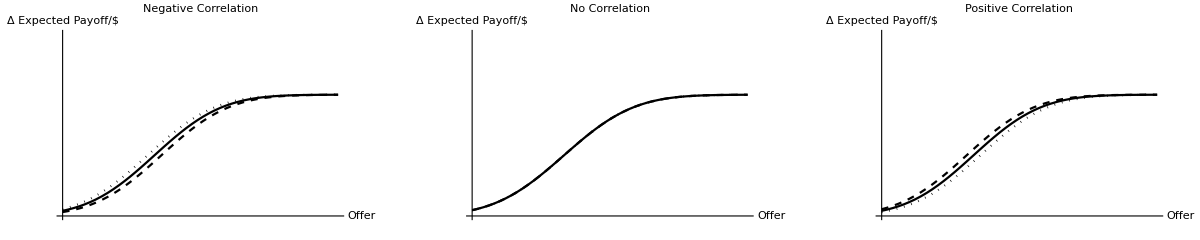

```mathematica
plotStyleList={{Black,Dashed},Black,{Black,Dotted}}; yRange={0,1.5}; 
plotOptions = {PlotStyle->plotStyleList,PlotRange->yRange,Ticks->None,AxesLabel->{"Offer","Δ Expected Payoff/$"}};
MCbySignal =GraphicsRow[{
Plot[{
pA[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
pA[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
pA[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Low Signal",PlotLegends-> Placed[{"ρ=-0.5","ρ= 0.0","ρ= 0.5"},{Scaled[{.65,.5}],{0,.5}}]],
Plot[{
pA[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
pA[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
pA[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Mean Signal",PlotLegends-> Placed[{"ρ=-0.5","ρ= 0.0","ρ= 0.5"},{Scaled[{.65,.5}],{0,.5}}]],
Plot[{
pA[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
pA[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
pA[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"High Signal",PlotLegends-> Placed[{"ρ=-0.5","ρ= 0.0","ρ= 0.5"},{Scaled[{.65,.5}],{0,.5}}]]
}
,ImageSize->Full]
MCbyCorrelation=GraphicsRow[{
Plot[{
pA[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
pA[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
pA[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Negative Correlation"],
Plot[{
pA[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
pA[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
pA[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"No Correlation"],
Plot[{
pA[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],
pA[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],
pA[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Positive Correlation"]}
,ImageSize->Full]
```

## Probability Marginal

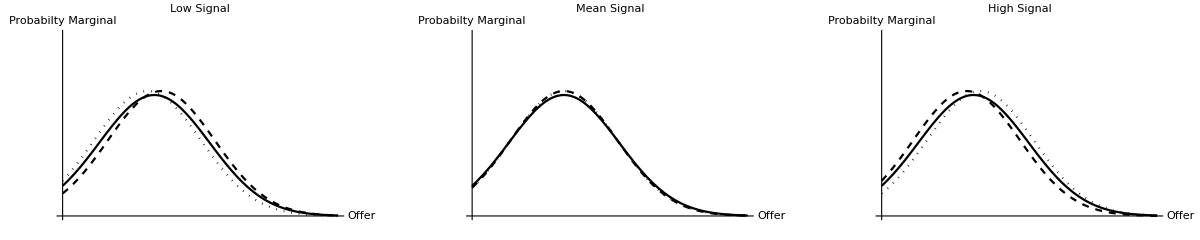

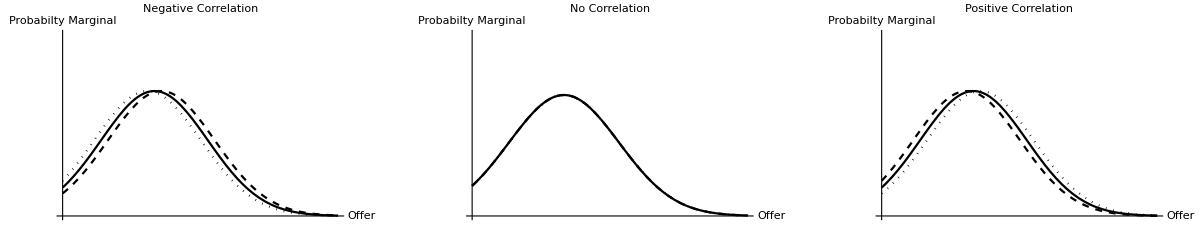

C:\Users\ssayre\Documents\activeProjectRepositories\esvcsV2\text\deltaPM.eps

```mathematica
plotStyleList={{Black,Dashed},Black,{Black,Dotted}}; yRange={0,2}; 
plotOptions = {PlotStyle->plotStyleList,PlotRange->yRange,Ticks->None,AxesLabel->{"Offer","Probabilty Marginal"}};
prMbySignal=GraphicsRow[{
Plot[{
pM[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
pM[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
pM[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Low Signal"],
Plot[{
pM[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
pM[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
pM[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Mean Signal"],
Plot[{
pM[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
pM[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
pM[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"High Signal"]
}
,ImageSize->Full]
pMbyCorrelation=GraphicsRow[{
Plot[{
pM[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
pM[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
pM[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Negative Correlation"],
Plot[{
pM[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
pM[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
pM[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"No Correlation"],
Plot[{
pM[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],
pM[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],
pM[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Positive Correlation"]}
,ImageSize->Full]
Export["C:\\Users\\ssayre\\Documents\\activeProjectRepositories\\esvcsV2\\text\\deltaPM.eps",pMbyCorrelation,"EPS"]
```

## Conditional Gain

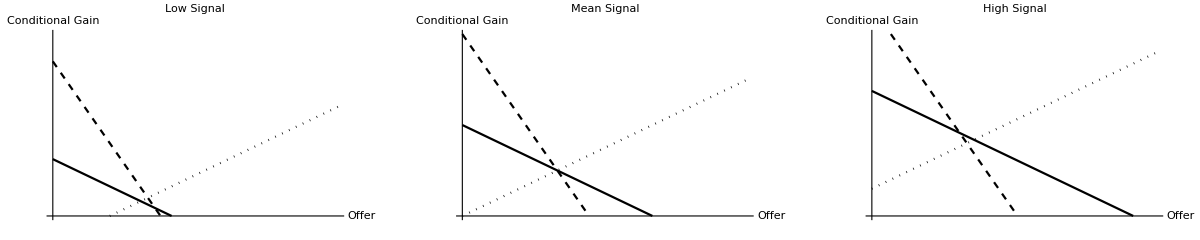

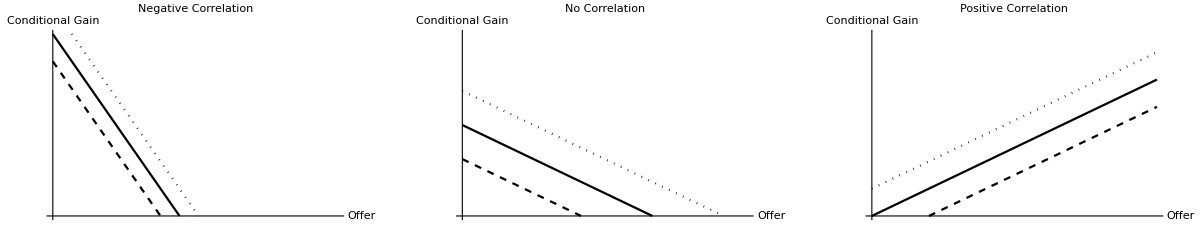

C:\Users\ssayre\Documents\activeProjectRepositories\esvcsV2\text\deltaCondGain.eps

```mathematica
plotStyleList={{Black,Dashed},Black,{Black,Dotted}}; yRange={0,2}; 
plotOptions = {PlotStyle->plotStyleList,PlotRange->yRange,Ticks->None,AxesLabel->{"Offer","Conditional Gain"}};
condGainBySignal=GraphicsRow[{
Plot[{
condGain[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
condGain[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
condGain[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Low Signal"],
Plot[{
condGain[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
condGain[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
condGain[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Mean Signal"],
Plot[{
condGain[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
condGain[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
condGain[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"High Signal"]
}
,ImageSize->Full]
condGainByCorrelation=GraphicsRow[{
Plot[{
condGain[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
condGain[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
condGain[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Negative Correlation"],
Plot[{
condGain[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
condGain[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
condGain[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"No Correlation"],
Plot[{
condGain[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],
condGain[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],
condGain[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Positive Correlation"]}
,ImageSize->Full]
Export["C:\\Users\\ssayre\\Documents\\activeProjectRepositories\\esvcsV2\\text\\deltaCondGain.eps",condGainByCorrelation,"EPS"]
```

## Marginal Benefit

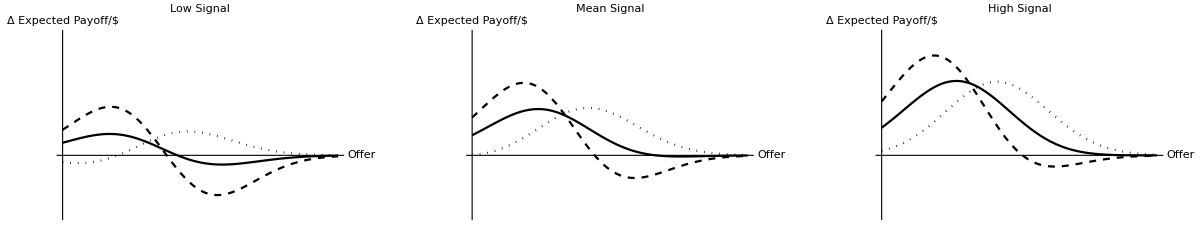

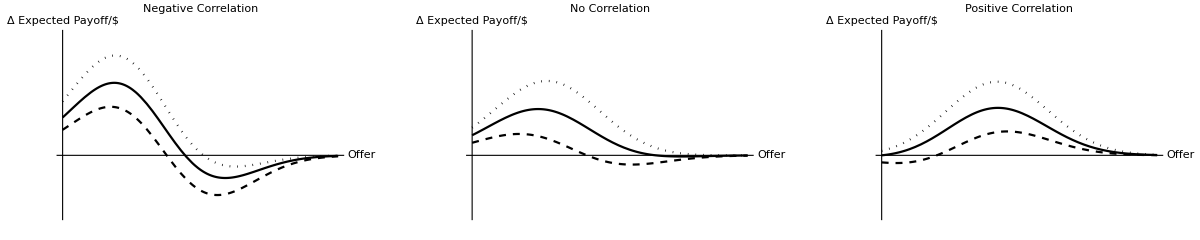

C:\Users\ssayre\Documents\activeProjectRepositories\esvcsV2\text\deltaMB.eps

```mathematica
plotStyleList={{Black,Dashed},Black,{Black,Dotted}}; yRange={-1,2}; 
plotOptions = {PlotStyle->plotStyleList,PlotRange->yRange,Ticks->None,AxesLabel->{"Offer","Δ Expected Payoff/$"}};
MBbySignal=GraphicsRow[{
Plot[{
MB[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Low Signal"],
Plot[{
MB[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Mean Signal"],
Plot[{
MB[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"High Signal"]
}
,ImageSize->Full]
MBbyCorrelation=GraphicsRow[{
Plot[{
MB[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Negative Correlation"],
Plot[{
MB[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"No Correlation"],
Plot[{
MB[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Positive Correlation"]}
,ImageSize->Full]
Export["C:\\Users\\ssayre\\Documents\\activeProjectRepositories\\esvcsV2\\text\\deltaMB.eps",MBbyCorrelation,"EPS"]
```

## Regulator Payoff Function

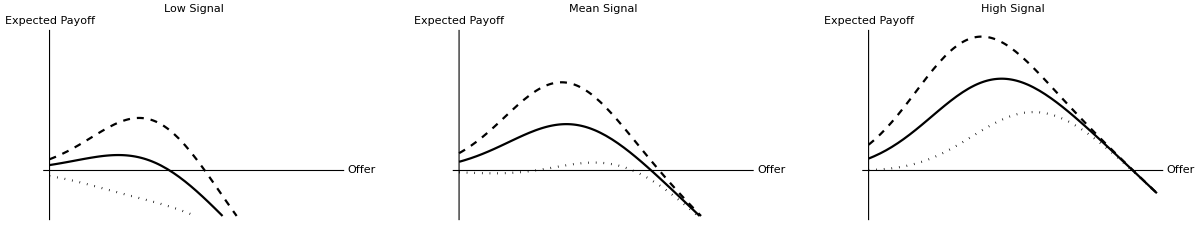

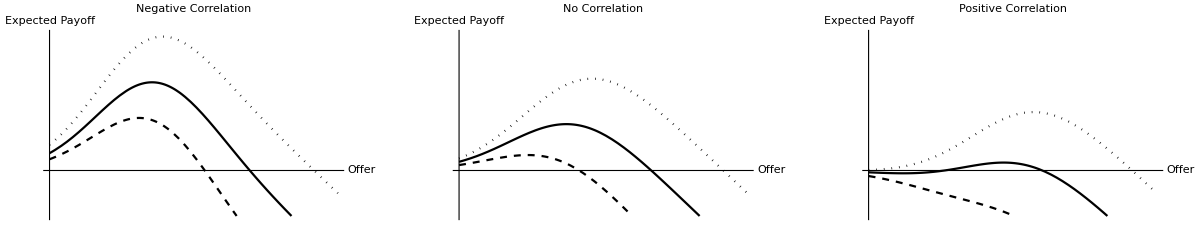

C:\Users\ssayre\Documents\activeProjectRepositories\esvcsV2\text\deltaPayoff.eps

```mathematica
plotStyleList={{Black,Dashed},Black,{Black,Dotted}}; yRange={-.25,.75}; 
plotOptions = {PlotStyle->plotStyleList,PlotRange->yRange,Ticks->None,AxesLabel->{"Offer","Expected Payoff"}};
rpfbySignal=GraphicsRow[{
Plot[{
rpf[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
rpf[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
rpf[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Low Signal"],
Plot[{
rpf[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
rpf[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
rpf[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Mean Signal"],
Plot[{
rpf[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
rpf[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
rpf[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"High Signal"]
}
,ImageSize->Full]
rpfbyCorrelation=GraphicsRow[{
Plot[{
rpf[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
rpf[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
rpf[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Negative Correlation"],
Plot[{
rpf[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
rpf[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
rpf[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"No Correlation"],
Plot[{
rpf[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],
rpf[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],
rpf[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Positive Correlation"]}
,ImageSize->Full]
Export["C:\\Users\\ssayre\\Documents\\activeProjectRepositories\\esvcsV2\\text\\deltaPayoff.eps",rpfbyCorrelation,"EPS"]
```